# Report containing a four-part introduction and some discussion about Enzyme Kinetics

## A computational study towards understanding enzyme kinetics

Emma Hokken 10572090
Natasja Wezel 11027649

## General Introduction

### 1. Michael-Menten Kinetics 2. Enzymes and inhibitors 3. Ionic channels

#### About ion channels

-Graphics-Figure 1: An Ion channel in closed and open state.
From: http://blog.canacad.ac.jp/wpmu/15matser/2011/09/14/4-1-passive-transport/

Cellular membranes contain ionic channels (see figure 1). These channels can be regarded as special enzymes for mediation ion transportation through the membrane. The channels considered here can exist in three states: S_1, S_2 and S_3. S_1 and S_3 represent closed states on either side of the membrane. When the channel is closed, no ions can pass trough the channel. S_2 is an open state. On a given cell, there are a number of channels and the fractions of channels in states S_1, S_2 and S_3 are designated x, y and z, respectively. These fractions lie between 0 and 1.

Transitions between the states go via the following schematic diagram:
S_1(⇌_k_3)^k_1 S_2→^k_2 S_3
Here, k_1,k_2 and k_3 are positive rate constants. The system of differential equations for this system is:

dx/dt=- k_1 x+k_3 y

dy/dt=k_1 x-(k_2+k_3) y

dz/dt=k_2 y

Methods 
To study the transitions between the different states of ion channels, firstly, we sketch the ion flow in the x,y plane, assuming that k_1=2, k_2=2 and k_3=1. Secondly, we solve the equations x, y and z as a function of time, starting from two different initial conditions: (1) x = 1, y = 0, z = 0; (2)  x = 0, y = 1, z = 0. Then, we solve the equations again, but with different rate constants: k_1=0, k_2=2 and k_3=1. We start from the second set of initial conditions we just defined. Furthermore, we then calculate x and z in terms of k_2 and k_3, assuming k_1=0 and k_2,k_3 are arbitrary positive numbers.

Results and Discussion

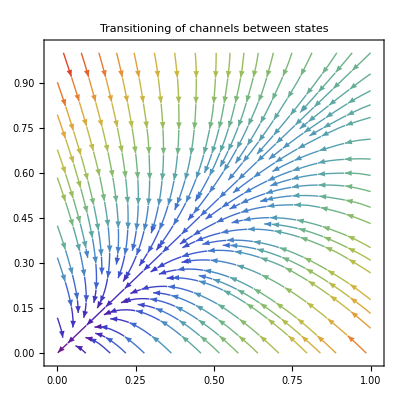

```mathematica
ClearAll["Global`*"]

dx[x_,y_]=-2 x+y;
dy[x_,y_]=2 x-(2+1) y;
dz[x_]=2 y;

StreamPlot[{dx[x,y],dy[x,y]},{x,0,1},{y,0,1}, PlotLabel->"Transitioning of channels between states", StreamColorFunction->"Rainbow"]
```

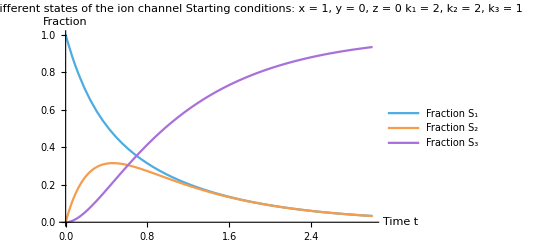

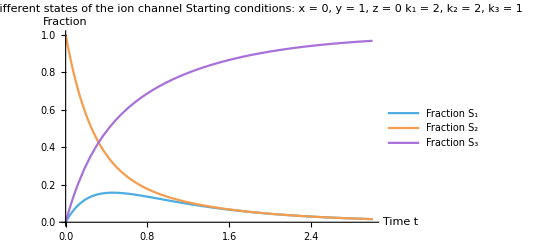

```mathematica
Remove[x, y, z]

solvedFirst[t_]=NDSolve[{x'[t]==-2 x[t]+y[t],y'[t]==2 x[t]-(2+1) y[t],z'[t]==2 y[t],x[0]==1,y[0]==0,z[0]==0},{x[t],y[t],z[t]},{t,0,3}];

solvedSecond[t_]=NDSolve[{x'[t]==-2 x[t]+y[t],y'[t]==2 x[t]-(2+1) y[t],z'[t]==2 y[t],x[0]==0,y[0]==1,z[0]==0},{x[t],y[t],z[t]},{t,0,3}];

Plot[Evaluate[{x[t]/.solvedFirst[t],y[t]/.solvedFirst[t],z[t]/.solvedFirst[t]}],{t,0,3},
AxesLabel->{"Time t", "Fraction"},
PlotLegends->{"Fraction S_1","Fraction S_2","Fraction S_3"},
PlotTheme->"Pastel",
PlotLabel-> "Population of different states of the ion channel\n Starting conditions: x = 1, y = 0, z = 0\n k_1 = 2, k_2 = 2, k_3 = 1"]

Plot[Evaluate[{x[t]/.solvedSecond[t],y[t]/.solvedSecond[t],z[t]/.solvedSecond[t]}],{t,0,3},
AxesLabel->{"Time t", "Fraction"},
PlotLegends->{"Fraction S_1","Fraction S_2","Fraction S_3"},
PlotTheme->"Pastel",
PlotLabel-> "Population of different states of the ion channel\n Starting conditions: x = 0, y = 1, z = 0\n k_1 = 2, k_2 = 2, k_3 = 1"]
```

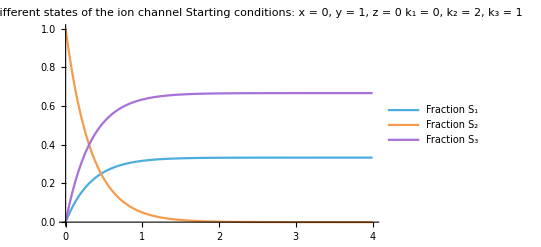

```mathematica
Remove[x,y,z]

solvedC1[t_]=NDSolve[{x'[t]==y[t],y'[t]==-(2+1) y[t],z'[t]==2 y[t],x[0]==0,y[0]==1,z[0]==0},{x[t],y[t],z[t]},{t,0,4}];

Plot[Evaluate[{x[t]/.solvedC1[t],y[t]/.solvedC1[t],z[t]/.solvedC1[t]}],{t,0,4},PlotLegends->{"Fraction S_1","Fraction S_2","Fraction S_3"}, PlotTheme->"Pastel", PlotLabel-> "Population of different states of the ion channel\n Starting conditions: x = 0, y = 1, z = 0\n k_1 = 0, k_2 = 2, k_3 = 1"]
```

```mathematica
Remove[x,y,z, k1, k2, k3]

DSolve[{x'[t]==k3*y[t],y'[t]==-(k2+k3)* y[t],z'[t]==k2 * y[t], x[0] == 0, y[0] == 1, z[0] == 0},{x[t],y[t],z[t]},t]
```

{{x[t]→-((-1+ⅇ^((-k2-k3) t)) k3)/(k2+k3),y[t]→ⅇ^((-k2-k3) t),z[t]→-((-1+ⅇ^((-k2-k3) t)) k2)/(k2+k3)}}

Conclusions
Hoi ik ga dingen concluderen